# University of Ottawa

## Assignment 3 - MOTION DETECTION IN IMAGE SEQUENCES

### Jana Rusrus (300205310)

ELG5163 - Machine Vision 						March 23 , 2021

### Temporal differentiation

The Temporal difference method is the simplest method for detecting temporal changes in intensity in frames.
It exhibits good performance in dynamic environments (e.g. during sunrise or under cloud cover) and works well at the standard video frame rate. the algorithm is easy to implement, with relatively
low design complexity, and can be executed effectively when applied to a real-time system.

As with static scenes, motion-based segmentation of moving scenes can rely on edge detection. However, intensity changes that result in edges, so called moving edges, now depend both on spatial variations and on temporal variations. Moving edges can be detected by a combination of the temporal and the spatial gradients. These static features are obstacles to extracting motion information.If only moving features are detected, the computation needed to perform matching may be substantially reduced.

The temporal gradient is : G(I(t)) = G_t = dI/dt,  and the spatial gradient is : G(I(x,y)) = (G_x
G_y) = (dI/dx
dI/dy)

combining both components : G(I(x,y,t)) = G(I(x,y)) G(I(t)). The product of the two gradient behaves as an AND operator.

A pixel-wise difference operator on successive frames is used to compute the temporal gradient:

Motion = Piecewise[{{1, if |I(x,y,t_1) - I(x,y,t_2)| > threshold}, {0, otherwise}}]

Edge detector will respond to slow-moving edges that have good edginess and to poor edges that are moving with appreciable speed. Another important fact about this detector is that it does not assume any displacement size The performance of the detector is satisfactory even when the motion of an edge is very large.

Temporal differencing is highly adaptive to dynamic environments; however, it generally exhibits poor performance in extracting all relevant feature pixels.

### Adaptive Background Subtraction

The concept underlying this method is to compute the average of the previous N frames to model the background, to update the first background image by considering new static objects in the scene. The background image is obtained as in Reference.
It’s a powerful mechanism for detecting change in a sequence of images that ﬁnds many applications. This method consumes a significant amount of memory, which causes problems for real-time implementation in particular.

motion(i, j, t) = image(i, j, t) - background(i,j,t-1)
if motion(i,j,t)>= threshold
	background(i,j,t) = background(i,j,t-1)
else
	background(i,j,t) = image(i,j,t)

### Improved method

I tried implementing two methods for improving the results of the previous methods. The first one was Three-frame Difference. and the second one is Optical flow . The first one is based on the temporal differencing method. Two difference operation are performed, then the results are thresholded and combined . The second one is trying to implement the optical flow (Figure 4), which can detect more objects than previous . For example, comparing Figure(2,3,4(g)), we can see that optical flow  detected the man in the left bottom which was not detected at all,  using temporal method and barely appeared detected in adaptive method.  However, the improvement was not very good due to the low frame rate, also using the median filter with 7 * 7 mask  smoothed the tiny details of the objects resulting in reducing the quality of detecting. There is a trade off  between noisy  image  ( because of salt and pepper noise )and smoothed image ( loosing the tiny details).

#### Note:

The result of the 3 methods is attached as a video called”video.avi”. [Top left is the input. Top right: result of temporal. Bottom left: result of Optical flow. Bottom right: result of  Adaptive.]

## Analysis

#### Performance

By looking at the results of both methods, we see that they both can detect objects but not perfectly, and we notice  some differences between the two.

Figure 1(a, b) shows the result  before applying any type of filters. We can see clearly the effect of salt and pepper noise in both methods. The noise was removed by applying 7 *7 Median filter as shown in Figure(2,3).

By looking at Figure(2,3)[a-b], we notice that both meth are quite similar. They both can predict similar things. For example, they can predict  the man in the bottom left,  and the vehicles in the same way.

We also notice that they both have some limitation. The shapes  can’t be  predicted accurately and fully, we can see some holes in objects. For instance, In Figure(2,3 [b]), the car at the top left , which has a lot of holes and even it’s not that much clear that it is a car. This problem was solved using the third improved method...............

Another limitation for both method related to the size of the object. I.e,  Objects with small sizes are not detected. For example, (Figure(2,3[8])), the pedestrians are not appeared. Also, when the contrast of the object is similar to the background one, a part of the object will be cut. For example (Figure(2,3[d,e])), we can notice that when the car in the right of the image  moves behind  the public phone booth, part of the car  affects the quality of detection.

Another

The threshold should be chosen carefully. If the threshold is smaller than the appropriate one, the objects will not be detected, and all the image will be noise(Figure 5.b). However, if the threshold is much larger (Figure5.c) than the suitable one, the objects will  have a lot of empty regions and holes and even they barely can be detected as an objects.

Some advantages of the Temporal differencing are  that  it considered one of  the simplest methods for detecting temporal changes in intensity in frames. It exhibits good performance in dynamic environments (e.g. during sunrise or under cloud cover) and works well at the standard video frame rate. the algorithm is easy to implement, with relatively low design complexity, and can be executed effectively when applied to a real-time system.

However,some disadvantages of it are : it generally exhibits poor performance in extracting all relevant feature pixels.

Some advantages of the Adaptive differencing are  that it’s one of  the most successful background subtraction methods apply probabilistic models to background intensities evolving in time; nonparametric and mixture-of-Gaussians models. Also,  it provides the most complete feature data.

However, Some disadvantages of it are this method consumes a significant amount of memory, which causes problems for real-time implementation in particular, Also, it’s difficult to select  robust detection threshold. In addition, it’s extremely sensitive to dynamic scene changes due to lighting and extraneous events.

## Appendix

## A sample Image from Temporal and Adaptive differentiation before applying filter.

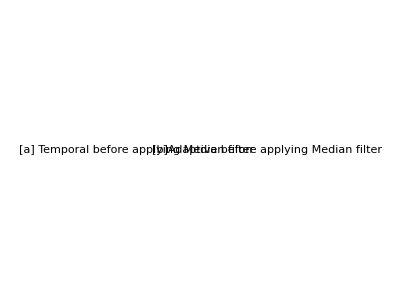

```mathematica
Block[{func,gauss},
func[imgLabel_]:=Labeled[
	Image[First[imgLabel],ImageSize->Scaled[0.5]],
	Last[imgLabel],
	Top,
	LabelStyle->Directive[Bold, Medium]
];
gauss={
{-Graphics-->"[a] Temporal before applying Median filter ",-Graphics-->"[b]Adaptive before applying Median filter  "}
};

GraphicsGrid[Map[func,gauss,{2}],ImageSize->Full,Spacings->0]
]
```

## Temporal differentiation

Figure(2): Results of Applying  Temporal differentiation with median filter on Image sequences.

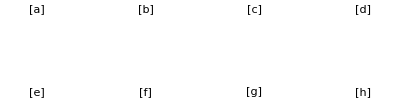

```mathematica
Block[{func,gauss},
func[imgLabel_]:=Labeled[
	Image[First[imgLabel],ImageSize->Scaled[0.9]],
	Last[imgLabel],
	Top,
	LabelStyle->Directive[Bold, Medium]
];
gauss={
{-Graphics-->"[a] ",-Graphics-->"[b] ",-Graphics- ->"[c] ", -Graphics-->"[d] "},
{-Graphics-->"[e] ",-Graphics-->"[f] ",-Graphics-->"[g] ",-Graphics-->"[h]"}
};

GraphicsGrid[Map[func,gauss,{2}],ImageSize->Full,Spacings->0]
]
```

## Adaptive differentiation

Figure(3): Results of Applying  Adaptive differentiation with median filter on Image sequences.

```mathematica
Block[{func,gauss},
func[imgLabel_]:=Labeled[
	Image[First[imgLabel],ImageSize->Scaled[0.9]],
	Last[imgLabel],
	Top,
	LabelStyle->Directive[Bold, Medium]
];
gauss={
{-Graphics-->"[a] ",-Graphics-->"[b] ", -Graphics-->"[c] ", -Graphics-->"[d] "},
{-Graphics-->"[e] ",-Graphics-->"[f]",-Graphics-->"[g]",-Graphics-->"[h] "}
};

GraphicsGrid[Map[func,gauss,{2}],ImageSize->Full,Spacings->0]
]
```

-Graphics-

## Optical Flow

Figure(4): Results of Applying  Optical Flow with median filter on Image sequences.

```mathematica
Block[{func,gauss},
func[imgLabel_]:=Labeled[
	Image[First[imgLabel],ImageSize->Scaled[0.9]],
	Last[imgLabel],
	Top,
	LabelStyle->Directive[Bold, Medium]
];
gauss={
{-Graphics-->"[a] ",-Graphics-->"[b] ",-Graphics- ->"[c] ", -Graphics-->"[d] "},
{-Graphics-->"[e] ",-Graphics-->"[f] ",-Graphics-->"[g] ",-Graphics-->"[h]"}
};

GraphicsGrid[Map[func,gauss,{2}],ImageSize->Full,Spacings->0]
]
```

-Graphics-

## Threshold

Figure(5): Results of choosing different thresholds.

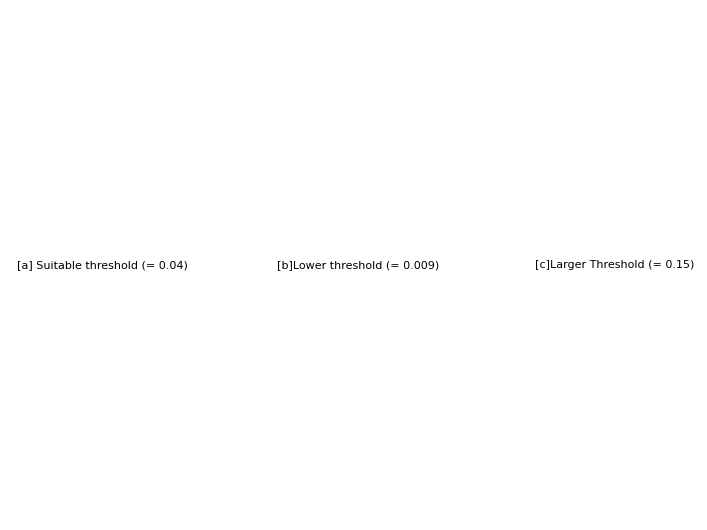

```mathematica
Block[{func,gauss},
func[imgLabel_]:=Labeled[
	Image[First[imgLabel],ImageSize->Scaled[0.9]],
	Last[imgLabel],
	Top,
	LabelStyle->Directive[Bold, Medium]
];
gauss={
{-Graphics-->"[a] Suitable threshold (= 0.04) ",-Graphics-->"[b]Lower threshold (= 0.009)  ",-Graphics-->"[c]Larger Threshold (= 0.15) "}
};

GraphicsGrid[Map[func,gauss,{2}],ImageSize->Full]
]
```